```mathematica
Needs["PlotLegends`"]
alpha = 1;
beta = 10;
fact[x_,n_]:=(alpha + beta*x^n/(1+x^n))/(alpha+beta);
frep[x_,n_]:=(alpha + beta*1/(1+x^n))/(alpha+beta)
```

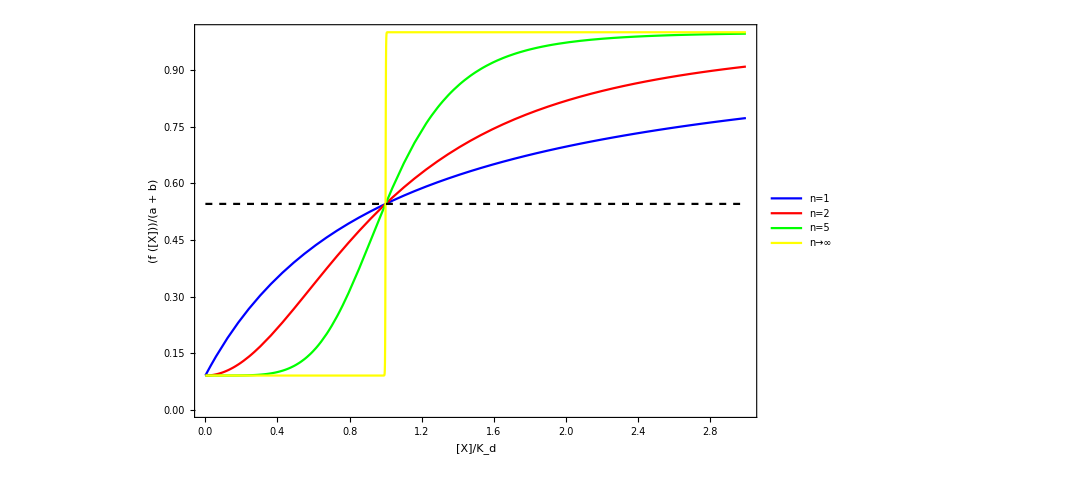

```mathematica
Plot[{fact[x,1],fact[x,2],fact[x,5], fact[x,1000], (alpha+0.5*beta)/(alpha+beta)},{x,0,3},ImageSize->800,Frame->True,FrameStyle->Black,FrameLabel->{"[X]/K_d","(f ([X]))/(a + b)"},RotateLabel->False,LabelStyle->Directive[18,FontFamily->"Palatino Linotype",Black],PlotStyle->{{Blue},{Red},{Green},{Yellow},{Black,Dashed}},PlotLegends->Placed[LineLegend[{"n=1","n=2","n=5","n→∞"},LabelStyle->{FontFamily->"Palatino Linotype",18},LegendLayout->{"Row",4},Spacings->0.2],{0.88,0.2}]]
```

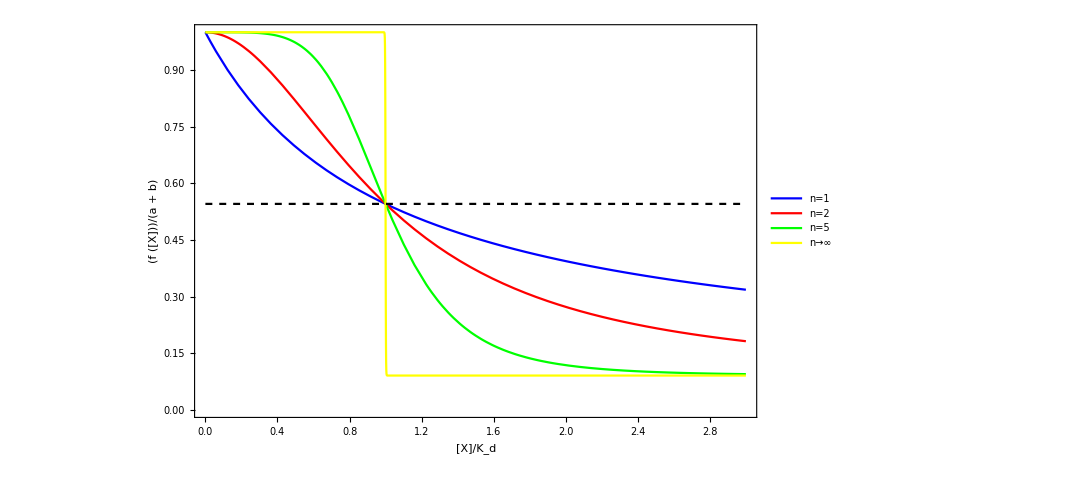

```mathematica
Plot[{frep[x,1],frep[x,2],frep[x,5], frep[x,1000], (alpha+0.5*beta)/(alpha+beta)},{x,0,3},ImageSize->800,Frame->True,FrameStyle->Black,FrameLabel->{"[X]/K_d","(f ([X]))/(a + b)"},RotateLabel->False,LabelStyle->Directive[18,FontFamily->"Palatino Linotype",Black],PlotStyle->{{Blue},{Red},{Green},{Yellow},{Black,Dashed}},PlotLegends->Placed[LineLegend[{"n=1","n=2","n=5","n→∞"},LabelStyle->{FontFamily->"Palatino Linotype",18},LegendLayout->{"Row",4},Spacings->0.2],{0.88,0.8}]]
```